## Langeving Simulation Multiplicative Noise

```mathematica
Clear[ξ,α]
```

```mathematica
d=0.1;
h=0.000;
T=2000;
dt=0.01;
nstep=T/dt;
ξtheor=4/d^2
```

400.

```mathematica
ξtheorExp=(4(d/2-1))^-1
```

1/(4 (-1+d/2))

```mathematica
proc=ItoProcess[ⅆx[t]==(d+1)*x[t]ⅆt-x[t]^3 ⅆt+h ⅆt+Sqrt[2]*x[t]*ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]];
```

```mathematica
ito=RandomFunction[proc,{0.,T,dt}]
```

TemporalData[<<1>>]

```mathematica
ListPlot[ito["Path"], PlotRange->All]
```

-Graphics-

```mathematica
manyReal=RandomFunction[proc,{0.,T,dt},10];
```

```mathematica
thermalized = manyReal["Part",All,{2*ξtheor,T}];
```

```mathematica
low=Ceiling[0.001*ξtheor/dt]
high=Ceiling[1.4*ξtheor/dt]/10;
corr=CorrelationFunction[thermalized,{low, high}]
logcorr=TimeSeries[Log[corr["Values"]],{corr["Times"]}];
```

40

TimeSeries[…]

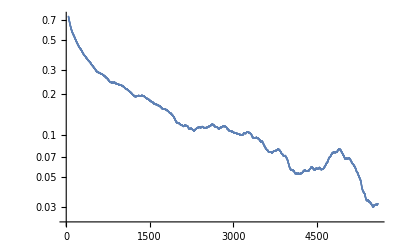

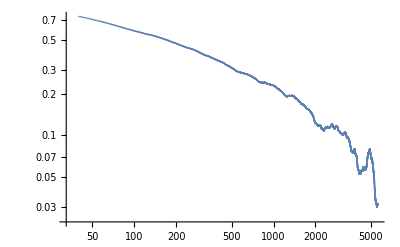

```mathematica
ListLogPlot[corr]
ListLogLogPlot[corr]
```

```mathematica
logcorr//Normal
```

{{40,-0.293325},{41,-0.298248},5558,{5600,-3.45434}}
 |  |  |  |

```mathematica
lm = LinearModelFit[logcorr//Normal,x,x];
-lm["BestFitParameters"][[2]]/dt
ξtheor/dt
```

0.0400729

40000.

```mathematica
lm["ParameterConfidenceIntervalTable"]
```

lm[ParameterConfidenceIntervalTable]

```mathematica
logExpPLM[x_,α_,β_,ξ_]:=α -x/ξ-β*Log[x]
```

```mathematica
nlmPL=NonlinearModelFit[logcorr,{logExpPLM[x,α,β,ξ],{α<10000,β>0.2,ξ>00}},{α,β,ξ},x]
nlmPL["ParameterConfidenceIntervalTable"]
```

FittedModel[«1»]

FittedModel::constr: The property values {ParameterConfidenceIntervalTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | Confidence Interval
α | 3.19453 | 0.0246771 | {3.14615,3.24291}
β | 0.699203 | 0.00319677 | {0.692936,0.70547}
ξ | 5.8623×10^10 | 6.87841×10^-20 | {5.8623×10^10,5.8623×10^10}

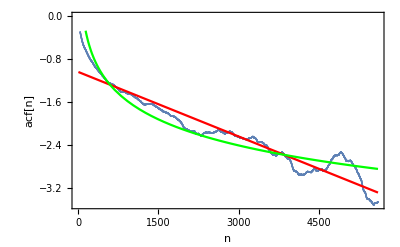

```mathematica
Show[ListPlot[logcorr],Plot[lm[x],{x,low/5,high},PlotStyle->Red],Plot[nlmPL[x],{x,low/5,high},PlotStyle->Green],Frame->True,FrameLabel->{"n","acf[n]"}]
```

```mathematica
CDFtheor[x_,d_] = (x^d (x^3)^(-d/3) (Gamma[d/3]-Gamma[d/3,x^3/2]))/Gamma[d/3];
```

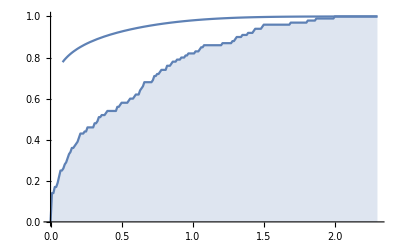

```mathematica
p1= DiscretePlot[CDF[thermalized["SliceDistribution",T],x],{x,0,2.3,0.01}];
p2= Plot[CDFtheor[x,0.5],{x,0,2.3}];
Show[p1,p2]
```

## Stochastic Logistic Model

```mathematica
slm=ItoProcess[ⅆx[t]==□/□*x[t]ⅆt-x[t]^3 ⅆt+h ⅆt+Sqrt[2]*x[t]*ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]];
```